```mathematica
fp[x_,μ_,σ_]=1/(√(2π)σ)Exp[-1/2(x-μ)^2/σ^2];
fc[x_,y_]=NIntegrate[1/(√(2π)σ)Exp[-1/2(x-μ)^2/σ^2] 1/(√(2π)√x)Exp[-1/2(x-y)^2/x],{y,-100,100}]
```

NIntegrate::inumr: The integrand (ⅇ^(-(x-y)^2/(2 x)-(x-μ)^2/(2 σ^2)))/(2 π √x σ) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-100,100}}.

NIntegrate[(Exp[-(x-μ)^2/(2 σ^2)] Exp[-(x-y)^2/(2 x)])/((√(2 π) σ) (√(2 π) √x)),{y,-100,100}]

NIntegrate::inumr: The integrand (ⅇ^(-(«19»-y)^2/(4 y)-(y-μ)^2/(2 σ^2)))/(2 √2 π √y σ) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1,100}}.

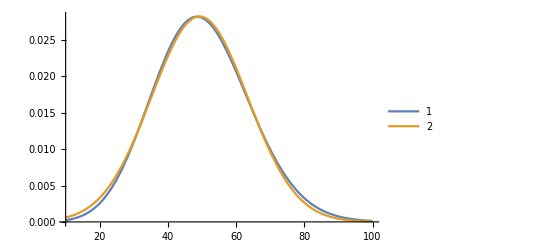

```mathematica
Plot[{NIntegrate[1/(√(2π)σ)Exp[-1/2(y-μ)^2/σ^2] 1/(√(2π)√(2y))Exp[-1/2(x-y)^2/(2 y)],{y,1,100}]/.{μ->50,σ->10},fp[x,49.24664962,14.12917836]},{x,10,100},PlotLegends->Automatic]
```